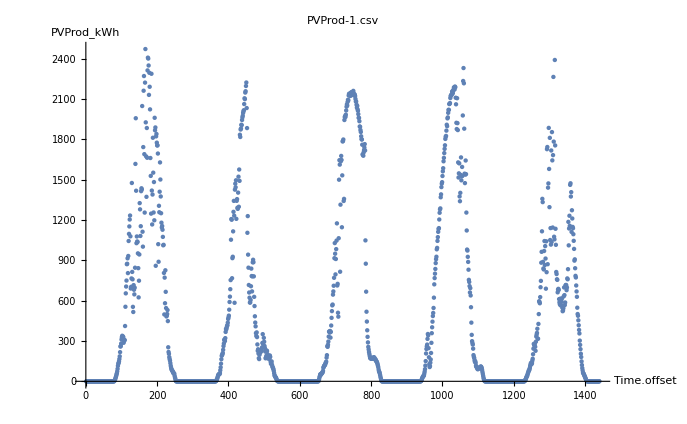

ARMAProcess[9.4326,{0.464027,0.241699,0.0393503,0.184388,0.174683,-0.12251},{0.349064},19905.8]

Piecewise[{{507142. 1.0094^(-1-Abs[s-t])-4621.43 2.30774^(-1-Abs[s-t])+2104.08 0.719265^Abs[s-t] Cos[0.139949-2.63338 Abs[s-t]]+7647.46 0.742712^Abs[s-t] Cos[0.324738-1.36968 Abs[s-t]], Abs[s-t]>0}, {509750., True}}]

12.6771

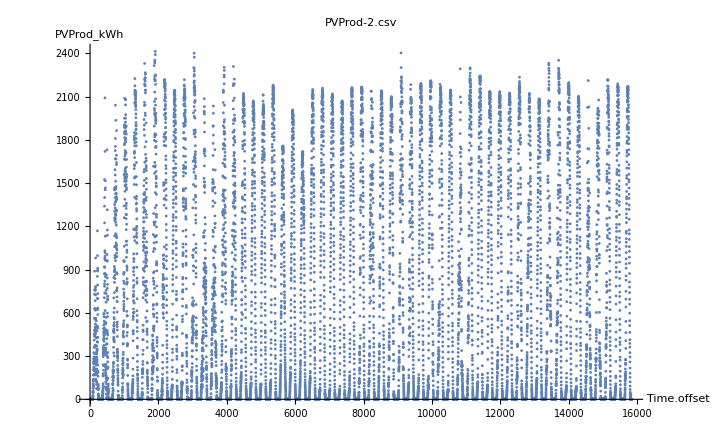

ARProcess[6.46721,{0.845912,0.143084},14047.1]

Piecewise[{{565837. 1.00971^(-1-Abs[s-t])+11059.3 (-1)^Abs[s-t] 6.9217^(-1-Abs[s-t]), Abs[s-t]>0}, {561995., True}}]

11.9379

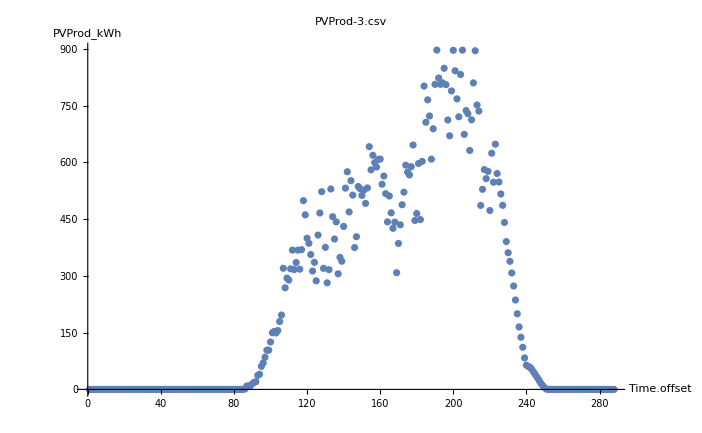

ARIMAProcess[4.95152×10^-16,{},1,{-0.198018,-0.134834},2913.11]

Piecewise[{{3080.29, s==0&&t==0}, {2581.22, s==0&&t==1}, {2188.44, s==0&&t==2}, {-392.785 (1+Min[0,-2+t])-499.069 (1+Min[0,-1+t])+3080.29 (1+Min[0,t]), s==0&&t>2}, {2581.22, s==1&&t==0}, {5162.45, s==1&&t==1}, {4270.59, s==1&&t==2}, {-392.785 (1+Min[1,-2+t])-499.069 (1+Min[1,-1+t])+3080.29 (1+Min[1,t])-499.069 Min[1,1+t], s==1&&t>2}, {2188.44, s==2&&t==0}, {4270.59, s==2&&t==1}, {6459.03, s==2&&t==2}, {-392.785 (1+Min[2,-2+t])-499.069 (1+Min[2,-1+t])+3080.29 (1+Min[2,t])-499.069 Min[2,1+t]-392.785 (-1+Min[2,2+t]), s==2&&t>2}, {3080.29 (1+Min[0,s])-499.069 Min[1,s]-392.785 (-1+Min[2,s]), s>2&&t==0}, {-499.069 (1+Min[0,s])+3080.29 (1+Min[1,s])-499.069 Min[2,s]-392.785 (-1+Min[3,s]), s>2&&t==1}, {-392.785 (1+Min[0,s])-499.069 (1+Min[1,s])+3080.29 (1+Min[2,s])-499.069 Min[3,s]-392.785 (-1+Min[4,s]), s>2&&t==2}, {-392.785 (1+Min[s,-2+t])-499.069 (1+Min[s,-1+t])+3080.29 (1+Min[s,t])-499.069 Min[s,1+t]-392.785 (-1+Min[s,2+t]), s>2&&t>2}, {0, True}}]

6.16132×10^-12

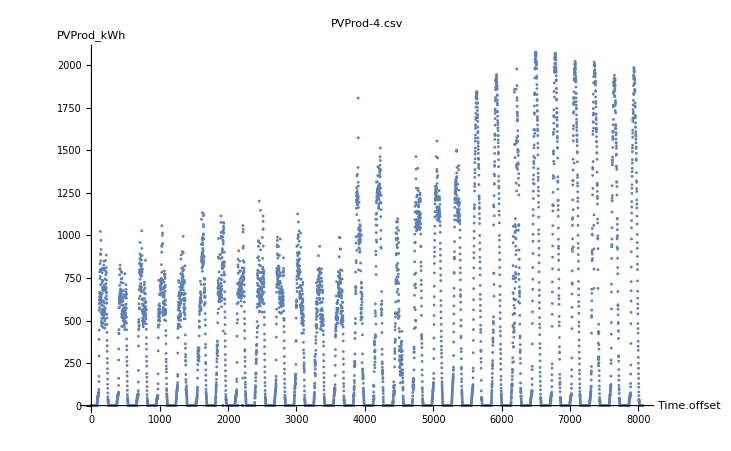

ARMAProcess[2.96659,{0.992128},{-0.143217},5642.92]

Piecewise[{{266251. 1.00793^(-1-Abs[s-t]), Abs[s-t]>0}, {264969., True}}]

6.4018

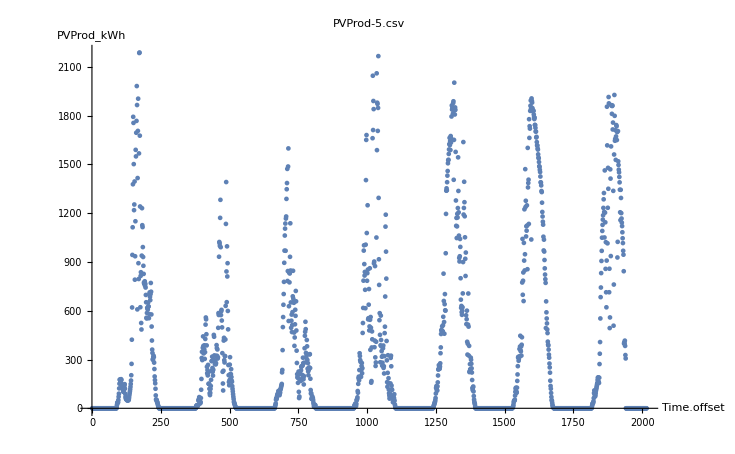

ARMAProcess[18.0821,{0.372286,0.570472},{0.703269},17522.5]

Piecewise[{{283349., Abs[s-t]==0}, {294664. 1.0373^(-1-Abs[s-t])-1214.25 (-1)^Abs[s-t] 1.6899^(-1-Abs[s-t]), True}}]

22.0343

```mathematica
ClearAll["Global`*"]

fitTimeseriesModel[f_,y_,z_]:=Module[{fname=f,yaxis=y,colnum=z},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/d4fa/PVProd/",fname],{"CSV","Data",All,{1,z}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}]; (* is 2 because only 2 data columns read *)
Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]];
atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
Print[CovarianceFunction[process,s,t]];
Print[TimeSeriesForecast[process,dataset[[All,2]], 2]];
];
(***********************************************)
 (* utc_timestamp, PVProd_kWh *)
col=3;
 fitTimeseriesModel["PVProd-1.csv","PVProd_kWh",col]; 
fitTimeseriesModel["PVProd-2.csv","PVProd_kWh",col];
fitTimeseriesModel["PVProd-3.csv","PVProd_kWh",col];
fitTimeseriesModel["PVProd-4.csv","PVProd_kWh",col];
fitTimeseriesModel["PVProd-5.csv","PVProd_kWh",col];
(***********************************************)
```